```mathematica
x=a+Exp[-k*x]/k Sin[k*(x+t)]
```

```mathematica
y=b-Exp[-k*x]/k Cos[k*(x+t)]
```

```mathematica
z=0
```

```mathematica
a=0;
```

```mathematica
b=0;
```

```mathematica
k=1;
```

```mathematica
t=0
```

0

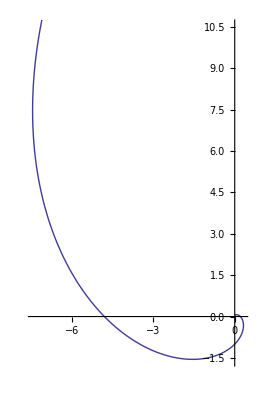

```mathematica
ParametricPlot[{a+Exp[-k*x]/k Sin[k*(x+t)],b-Exp[-k*x]/k Cos[k*(x+t)]},{x,-Pi,Pi},PlotRange->Automatic]
```

```mathematica
Animate[Manipulate[ParametricPlot[{a+Exp[-k*x]/k Sin[k*(x+t)],b-Exp[-k*x]/k Cos[k*(x+t)]},{x,0,10*Pi},PlotRange->Automatic],{k,.01*Pi,Pi/2}],{t,0,10}]
```

```mathematica
This can be performed in 3D as well.
```

```mathematica
ParametricPlot3D[{a+Exp[-k*x]/k Sin[k*(x+t)],b-Exp[-k*x]/k Cos[k*(x+t)],0},{x,.01*Pi,Pi/2},PlotRange->Automatic]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{a+Exp[-k*x]/k Sin[k*(x+t)],b-Exp[-k*x]/k Cos[k*(x+t)],a+Exp[-k*x]/k Sin[k*(x+t)]},{x,.01*Pi,Pi/2},PlotRange->Automatic]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{a+Exp[-k*x]/k Sin[k*(x+t)],b-Exp[-k*x]/k Cos[k*(x+t)],b-Exp[-k*x]/k Cos[k*(x+t)]},{x,.01*Pi,Pi/2},PlotRange->Automatic]
```

-Graphics3D-

```mathematica
Clear[t]
```

```mathematica
Manipulate[ContourPlot[{a+Exp[-k*x]/k Sin[k*(x+t)],b-Exp[-k*x]/k Cos[k*(x+t)]},{x,.01*Pi,Pi*2},{k,1,10},PlotRange->{-1,1},WorkingPrecision->10^2],{t,0,10}]
```

```mathematica
Manipulate[ParametricPlot3D[{a+Exp[-k*x]/k Sin[k*(x+t)],b-Exp[-k*x]/k Cos[k*(x+t)],0},{x,.01*Pi,Pi*2},PlotRange->{-1,1}],{t,0,10},{k,1,10}]
```

```mathematica
Manipulate[ParametricPlot3D[{a+Exp[-k*x]/k Sin[k*(x+t)],b-Exp[-k*x]/k Cos[k*(x+t)],Sinh[x]},{x,.01*Pi,Pi*2},PlotRange->{-1,1}],{t,0,10},{k,1,10}]
```

```mathematica
What is the symmetry of these functions when a and b are equal? How does that relate to when they are both zero?
```

```mathematica
It is most interesting when creating a degeneracy with either the x or y direction(z=y or z=x).
```

```mathematica
Furthermore, one can manipulate the z axis into arbitrary functions in this case the Sinh[z],
```

```mathematica
Clear[a,b,k,t]
```

```mathematica
a=0;
```

```mathematica
b=0;
```

```mathematica
k=1;
```

```mathematica
t=0
```

0

```mathematica
Manipulate[ParametricPlot[{a+Exp[-k*x]/k Sin[k*(x+t)],b-Exp[-k*x]/k Cos[k*(x+t)]},{x,-2*Pi,2*Pi},PlotRange->{-25,25}],{a,0,10},{b,0,10},{k,1,2*Pi},{t,0,5}]
```

```mathematica
For k less than 1:
```

```mathematica
Manipulate[ParametricPlot[{a+Exp[-k*x]/k Sin[k*(x+t)],b-Exp[-k*x]/k Cos[k*(x+t)]},{x,-2*Pi,2*Pi},PlotRange->{-25,25}],{a,0,10},{b,0,10},{k,.001,1},{t,0,5}]
```